```mathematica
ClearAll["Global`*"]
```

```mathematica
Adata={76,82,96,100,116,128,130,150};
DeltaP={0.607,1.289,0.694,2.138,0.177,2.142,1.879,1.359};
(* daughter *)
SQRTA={1.376,1.325,1.224,1.2,1.114,1.061,1.052,0.979};
(*1/2sqrtA*)
```

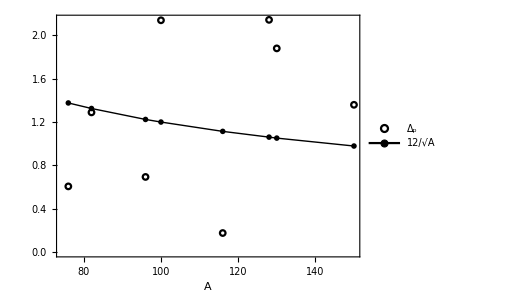

```mathematica
plot=ListPlot[{Table[{Adata[[i]],DeltaP[[i]]},{i,1,Length[Adata]}],Table[{Adata[[i]],SQRTA[[i]]},{i,1,Length[Adata]}]},Joined->{False, True},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],LabelStyle->{22,Bold,Black,FontFamily->"Times"},FrameLabel->{"A"},PlotRange->All,PlotStyle->{{Black},{Black,Thick}},PlotMarkers->{{Graphics[{Circle[]}],1/18},{Graphics[{Disk[]}],1/20}},PlotLegends->Placed[{"Δ_p","12/√A"},{0.8,0.18}],ImageSize->380];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/Delta-plots/figure-3/figure-3.pdf",Show[plot],ImageResolution->1200];
Show[plot]
```